Metody numeryczne, Informatyka NS sem. III, 2023/2024

Andrzej Manderla

# Projekt 4 – interpolacja Lagrange’a

## KOD

```mathematica
lagrangeInterpolation[f_,a_,b_,n_]:=Module[{xValues,yValues,w=0,ϕ},
xValues=Table[a+Abs[(a-b)]/(n-1)*i,{i,0,n-1}];
yValues=Table[f[xValues[[i]]],{i,1,Length[xValues]}];
For[i=1,i<=n,i++,ϕ=1;
For[k=1,k<=n,k++,If[i!=k,ϕ=ϕ*(x-xValues[[k]])/(xValues[[i]]-xValues[[k]])];];
w=w+yValues[[i]]*ϕ;];
Print["Polynomial: ",Simplify[w//N]];
Print[Show[Plot[{w,f[x]},{x,xValues[[1]],xValues[[n]]},PlotStyle->{Directive[Green,Dashed],Directive[Orange,Thin]},PlotRange->Full,Background->White],ListPlot[Thread[{xValues,yValues}]]]];
Print[Plot[Abs[f[x]-w],{x,xValues[[1]],xValues[[n]]},PlotStyle->Green,PlotRange->Full,Background->White]];];
```

## Przykłady

### Przykład z przykładowych przykładów.

Polynomial: -1.+5. x-9.7615 x^2+4.86342 x^3-0.688033 x^4

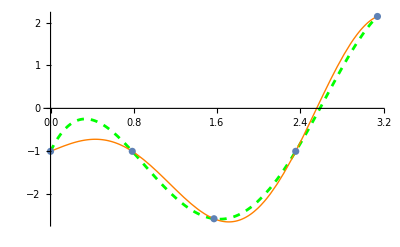

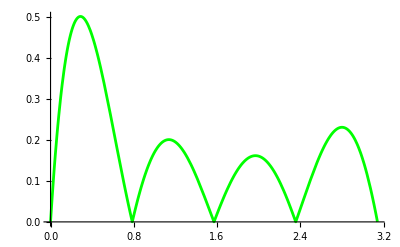

```mathematica
f[x_]:=x Cos[2x]-1;
lagrangeInterpolation[f,0,Pi,5]
```

### Przykład własny.

Polynomial: 0.+1.69765 x-0.810569 x^2+0.0860041 x^3

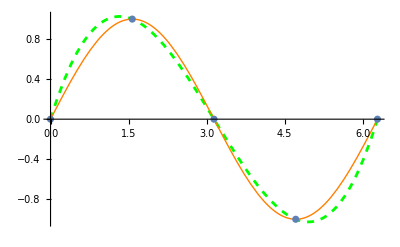

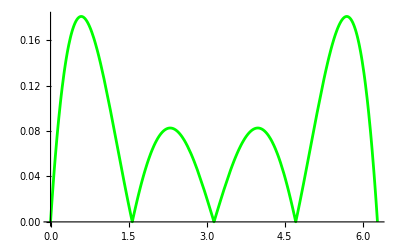

```mathematica
f[x_]:=Sin[x];
lagrangeInterpolation[f,0,2Pi,5]
```